```mathematica
SetOptions[#,Axes->False,Frame->True]&/@{ListPlot,ListLinePlot,Plot};
SetDirectory[NotebookDirectory[]]
```

C:\Users\akandra\git\kmc_tian

```mathematica
data=Import["mmc_test1.confs","Table"];
{nlat,nads}=data[[1]]
occs=Partition[data[[2;;]],nlat];
nframes=Length[occs]
```

{100,6500}

1001

```mathematica
energy=Import["mmc_test1.en","List"];
```

```mathematica
data=Import["mmc_test2.confs","Table"];
{nlat2,nads2}=data[[1]]
occs2=Partition[data[[2;;]],nlat2];
nframes2=Length[occs2]
```

{100,6500}

1001

```mathematica
energy2=Import["mmc_test2.en","List"];
```

```mathematica
data=Import["mmc_test3.confs","Table"];
{nlat3,nads3}=data[[1]]
occs3=Partition[data[[2;;]],nlat3];
nframes3=Length[occs3]
```

{100,6500}

1001

```mathematica
energy3=Import["mmc_test3.en","List"];
```

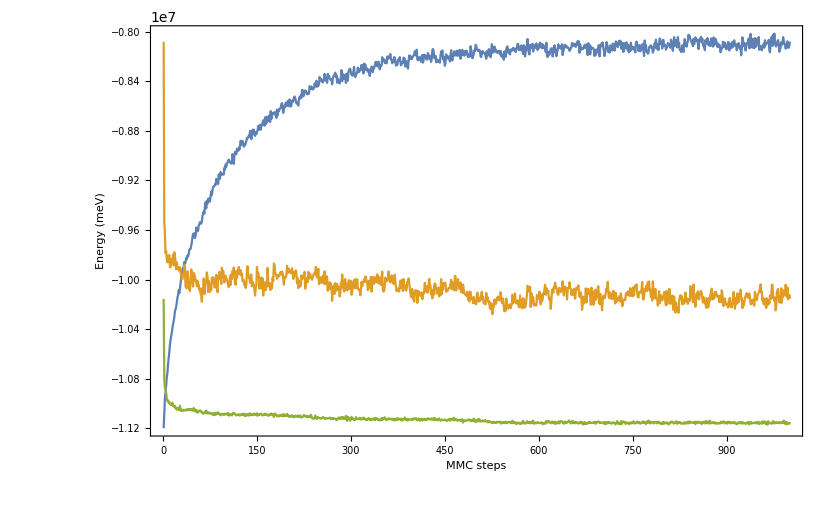

```mathematica
ListLinePlot[{energy,energy2,energy3},PlotRange->All,FrameLabel->{"MMC steps","Energy (meV)"}]
```

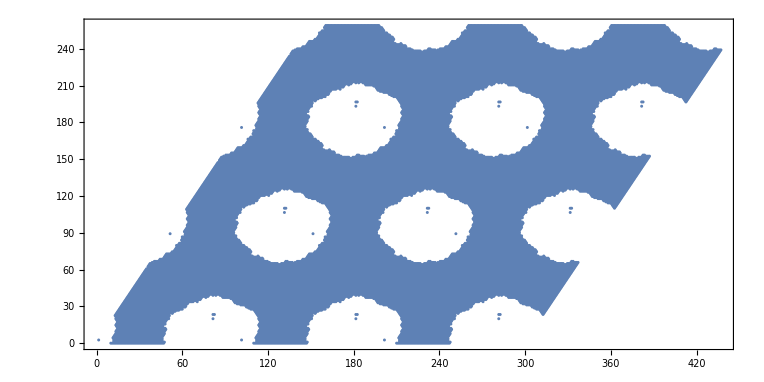

```mathematica
ListPlot[(((#-{1,1})&/@Position[ArrayPad[occs3[[-1]],nlat,"Periodic"],1]).{{1,0},{Cos[π/3],Sin[π/3]}}),AspectRatio->Cos[π/3]]
```

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs3[[i]],nlat,"Periodic"],ColorFunction->"Monochrome"],{i,1,nframes,1}]
```

```mathematica
Manipulate[MatrixPlot[ArrayPad[occs3[[i]],0,"Periodic"],ColorFunction->"Monochrome"],{i,1,nframes,1}]
```